```mathematica
(*S[n_,m_,z_]:=(√(n! m!))/Cosh[z]^(n+1/2)(Tanh[z]/2)^((m-n)/2)F[n,m,z] Cos[(n-m)π/2]^2;*)
S[n_,m_,z_]:=(√(n! m!))/Cosh[z]^(n+1/2)(Tanh[z]/2)^((m-n)/2)(∑_(k=(n-m)/2)^(n/2) ((-1)^k(Sinh[z]/2)^(2k))/(k! (n-2k)!((m-n)/2+k)!))Mod[Abs[n-m],2];
Sd[n_,m_,z_]:=S[n,m,-z];
(*F[n_,m_,z_]:=∑_(k=(n-m)/2)^(n/2) ((-1)^k(Sinh[z]/2)^(2k))/(k! (n-2k)!((m-n)/2+k)!);*)
F[n_,m_,z_]:=(2^(m-n) Hypergeometric2F1Regularized[(1-m)/2,-m/2,1/2 (2-m+n),-Sinh[z]^2] (ⅈ Sinh[z])^(-m+n))/(m!);
ρ[n_,m_,α_]:=ⅇ^(-α^2)(α^n(α*)^m)/(√(n! m!));
```

```mathematica
GoodPart=∑_(n=0)^∞ (1-η)^n∑_(p=0)^∞ S[n,p,z]ρ[p,0,α]Sd[0,n,z]
```

```mathematica
∑_(p=0)^∞ S[n,p,z]ρ[p,0,α]S[0,n,-z]
```

∑_(p=0)^∞ 1/((p!)^(3/2) (1/2 (-p+z))!)ⅈ^(-p+z) 2^(-n/2+(n-p)/2+p-z) ⅇ^(-α^2) α^p Cos[(n π)/2]^2 Cos[1/2 (n-p) π]^2 Cosh[z]^(-1-n) √(n!) √(n! p!) Hypergeometric2F1[1/2-p/2,-p/2,1-p/2+z/2,-Sinh[n]^2] Sinh[n]^(-p+z) (∑_(k=1/2 (-n-z))^(-z/2) ((-1)^k 0^(2 k))/(k! (-2 k-z)! (k+(n+z)/2)!)) (-Tanh[z])^(n/2) Tanh[z]^(1/2 (-n+p))

```mathematica
S[n,p,z]ρ[p,0,α]S[0,n,-z]
```

1/(n/2! (n-p)/2! (p!)^(3/2))ⅈ^(n-p) 2^(-(3 n)/2+(n-p)/2+p) ⅇ^(-α^2) α^p Cosh[z]^(-1-n) √(n!) √(n! p!) Hypergeometric2F1[1/2-p/2,-p/2,1+n/2-p/2,-Sinh[z]^2] Mod[Abs[n],2] Mod[Abs[n-p],2] Sinh[z]^(n-p) (-Tanh[z])^(n/2) Tanh[z]^(1/2 (-n+p))

```mathematica
ClearAll[generalsum];
generalsum[n_,p_,q_,z_,α_]:=S[n,p,z]ρ[p,q,α]S[q,n,-z];
```

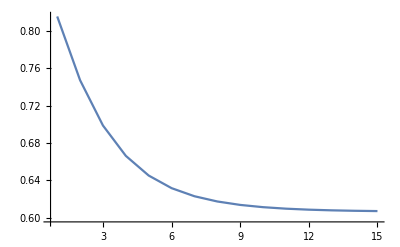

```mathematica
ListLinePlot[((N[∑_(n=0)^2 ((1-η)^n∑_(p=0)^20 generalsum[n,p,0,#,α])]/N[∑_(n=0)^2 ((1-η)^n∑_(p=0)^20 ∑_(q=0)^20 generalsum[n,p,q,#,α])])/.{η->0.8,α->1})&/@Range[0.01,3,.2],PlotRange->Full]
```

```mathematica
(*Squeezing is not helping! *)
```